# Signalverarbeitung UE2 - Notebook

## 1)

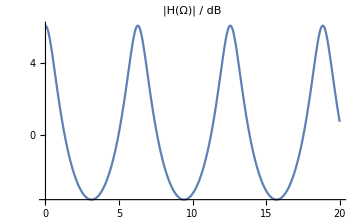
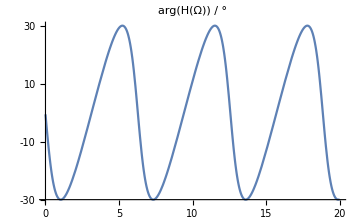

```mathematica
BodePlot[1/(1-0.5Exp[-ⅈω]), {0.01, 20},
ImageSize->Medium,
PlotLayout->"List",
PlotLabel->{"|H(Ω)| / dB","arg(H(Ω)) / °"},
Frame->False,
ScalingFunctions->{{"Linear", Automatic}, {"Linear", Automatic}}]
```

```mathematica
FullSimplify[(1-Exp[-ⅈΩ])/(1-0.5Exp[-ⅈΩ])]
```

(-1.+ⅇ^ⅈΩ)/(-0.5+ⅇ^ⅈΩ)

## 2)

### b und d)

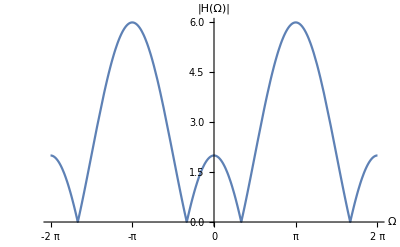

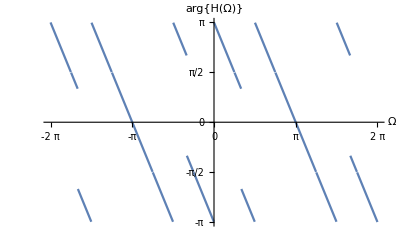

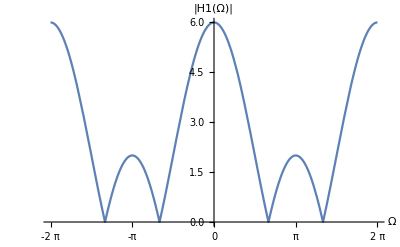

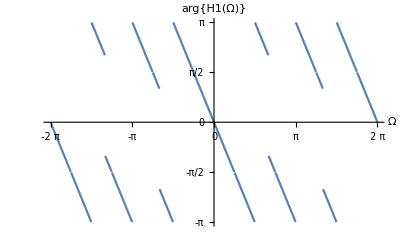

```mathematica
H [Ω_]:= 2(Cos[2Ω]-Cos[Ω]-Cos[3Ω])-ⅈ 2 (Sin[2Ω]-Sin[Ω]-Sin[3Ω])

Plot[Abs[H[Ω]],{Ω,-2Pi, 2Pi},AxesLabel -> {"Ω","|H(Ω)|"},Ticks->{Range[-2Pi,2Pi,Pi],Automatic}]
Plot[Arg[H[Ω]],{Ω,-2Pi, 2Pi},AxesLabel -> {"Ω","arg{H(Ω)}"},Ticks->{Range[-2Pi,2Pi,Pi], Range[-Pi,Pi,Pi/2]}]

Plot[Abs[H[Ω+Pi]],{Ω,-2Pi, 2Pi},AxesLabel -> {"Ω","|H1(Ω)|"},Ticks->{Range[-2Pi,2Pi,Pi],Automatic}]
Plot[Arg[H[Ω+Pi]],{Ω,-2Pi, 2Pi},AxesLabel -> {"Ω","arg{H1(Ω)}"},Ticks->{Range[-2Pi,2Pi,Pi], Range[-Pi,Pi,Pi/2]}]
```

## 3)

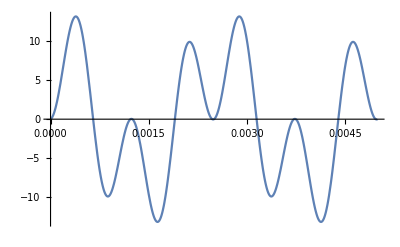

```mathematica
ω1 = 2Pi*400;
ω2=2Pi*800;
ω3 = 2Pi*1600;
x[t_] := 5Sin[ω1*t]3Sin[ω2*t]+2Sin[ω1*t]
Plot[x[t],{t,0,0.005}]
```